#### Tarea: Programar mi primer caminata cuántica, implementando gráficas de probabilidad y desviación estándar en función del tiempo y en específico, intentar replicar las gráficas 3.5 y 3.6 del libro. -Graphics--Graphics-

Primero, definiremos nuestros parámetros iniciales, como en la gráfica 3.5 se nos muestra la distribución después de 100 pasos (Tmax) directamente utilizaremos eso.
En una QW,  el caminate se mueve una unidad hacia cualquier dirección y sabemos que la posición (partiendo de n = 0) siempre la encontraremos entre [-t, +t] ,  tendremos entonces 2t +1 posibles posiciones (llamaremos L al espacio de posiciones y LP a la lista [-t, +t]).
Además denotamos al operador de moneda Hadamar como H

```mathematica
Tmax = 100;
L = 2*Tmax + 1;
LP = Range[-Tmax, Tmax];
H = (1/Sqrt[2]){{1,1},{1,-1}};
```

Nosotros queremos “condicionar” el movimiento del caminante dependiendo del valor de la moneda, para esto es necesario recordar que trabajamos con espacios de Hilbert y específicamente el espacio moneda es de base {|0>, |1>}. Necesitamos los operadores |0> y |1> para saber a dónde se mueve el caminante (derecha o izquierda, respectivamente), haremos entonces una proyección sobre ellos mismos

```mathematica
P0 = {{1,0}, {0,0}}; (* |0><0| *)
P1 = {{0,0}, {0,1}}; (* |1><1| *)
```

Ya que definimos todo lo anterior, veamos cómo es el movimiento del caminante. 
Para esto recordemos el operador Shift (u matriz de desplazamiento), si en el operador moneda tenemos |0> iremos a la derecha de una posición n a una posición n+1 y si el operador moneda tenemos |1> iremos a la izquierda desde una posición n a una n-1. 
Tendremos la transformación |i> -> |i + 1> y  |i> -> |i + 1>

```mathematica
SR = SparseArray[Table[{i + 1, i} -> 1, {i, 1, L-1}], {L,L}]; (*desplazamiento a la derecha*)
SL= SparseArray[Table[{i-1, i} -> 1, {i, 2, L} ], {L,L}];(*desplazamiento a la izquierdA*)
```

De estos dos operadores obtenemos un operador “completo” , combinamos (Kronecker; moneda, posición) las proyecciones con los desplazamientos (por definición de la matriz de desplazamiento.

```mathematica
SC = KroneckerProduct[P0, Normal[SR]] + KroneckerProduct[P1, Normal[SL]];
```

Ya que construimos la matriz de desplazamiento podemos obtener el operador de evolución U = S(H x I)

```mathematica
U = SC. KroneckerProduct[H, IdentityMatrix[L]];
```

En el caso de la figura 3.3 se nos dice que tenemos un estado inicial, el cual es

```mathematica
M0=(1/Sqrt[2]) {1,-I}; (*(|0>-i|1>)/sqrt(2), estado inicial de la moneda*)
PI0=(L+1)/2;(*n=0*)
pos0=SparseArray[{PI0->1},{L}];  (*estado de posición en n=0*)
psi0=Flatten[KroneckerProduct[M0,pos0]]; (*Estado global, producto tensorial moneda x posivion*)
```

Todos los estados estarán dados por la siguiente lista

```mathematica
states = NestList[U.# &, psi0, Tmax];
```

Hasta aquí, ya hemos definido la evolución del sistema. Ya podemos empezar a calcular probabilidad, distribución... 
Primero, organizremos los posibles estados en una matriz 2xL (HC = 2D y Hp = LD)

```mathematica
reshape[stateVec_]:=ArrayReshape[stateVec,{2,L}];
```

Ahora podemos pasar a la distribución de probabilidades de las posiciones

```mathematica
ProbP[stateVec_]:=Module[{m=reshape[stateVec]},
Total[Abs[m]^2,{1}]];
```

Calculamos hora la desviación estándar usando la distribución de probabilidades anterior

```mathematica
stdFromState[stateVec_]:=Module[{p=ProbP[stateVec],mean,mean2},
mean=Total[LP*p]; (*media*)
mean2=Total[(LP^2)*p]; (*valor medio cuadratico*)
Sqrt[mean2-mean^2]]; (*raiz de la varianza*)
```

Ya tenemos todo para empezar a construir nuestras gráficas, primero iniciaremos con la figura 3.5

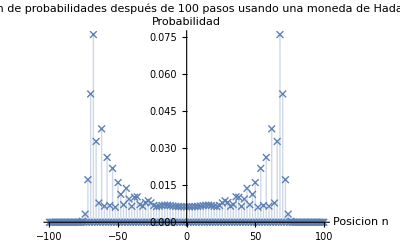

```mathematica
prob100=ProbP[states[[101]]];  (* 101 porque states empieza en t=0*)
fig35=ListPlot[Transpose[{LP,prob100}],
Filling->Axis,
PlotRange->All,
Joined->False,
PlotMarkers->{"×",7},
AxesLabel->{"Posicion n","Probabilidad"},PlotLabel ->"Distribución de probabilidades después de 100 pasos usando una moneda de Hadamard."];
fig35
```

Ahora intentaremos replicar la imagen 3.6

```mathematica
QStdL=Table[stdFromState[states[[t+1]]],{t,0,Tmax}];  
CStdL=Table[Sqrt[t],{t,0,Tmax}];                    (*sigma=sqrt(t)*)

Ps=Range[0,Tmax];
```

Con esto ya podemos construir la figura

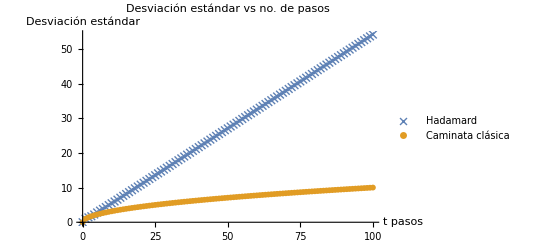

```mathematica
fig36=ListPlot[{Transpose[{Ps,QStdL}],(*ruces*)
Transpose[{Ps,CStdL}]   (*círculos*)},
PlotStyle->{Thick,Dashed},
PlotMarkers->{{"×",8},{"●",6}},
Joined->False,
AxesLabel->{"t pasos","Desviación estándar"},PlotLegends->{"Hadamard","Caminata clásica"},PlotLabel->"Desviación estándar vs no. de pasos"];
fig36
```